```mathematica
(*Import packages*)
(*<< PVReduce`*)
(*Remove[PVReduce`Dot];*)
$LoadAddOns={"FeynArts"};
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<< TreeLevel`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

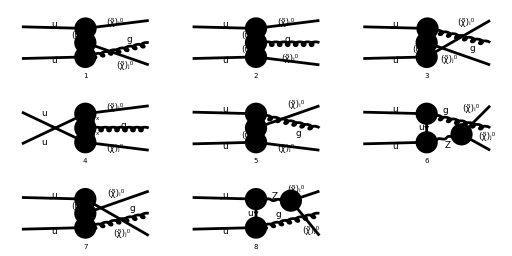

```mathematica
EmissionDiagrams = InsertFields[CreateTopologies[0, 2->3], {F[3, {1,α}], -F[3, {1,β}]} -> {F[11, {i}],V[5,{a}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD,Restrictions->{NoLightFHCoupling,NoElectronHCoupling}];
Paint[EmissionDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

```mathematica
Subscript[M, gluon][0]=FCFAConvert[CreateFeynAmp[EmissionDiagrams], IncomingMomenta->{p1,p2}, OutgoingMomenta->{pi,k,pj},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν}]//.AmpSimplifyRules;
```

```mathematica
Subscript[M, gluon][1]=Subscript[M, gluon][0]/.ZSimplifyRules/.QSimplifyRules/.SuperChargeRules//Simplify;
```

```mathematica
Subscript[M̄, gluon][1]=ConjugateAmplitude[Subscript[M, gluon][1]];
```

```mathematica
FCClearScalarProducts[];
ScalarProduct[k,k]=0;
SetMandelstam[m2,{p1,p2,-pi,-pj,-k},{0,0,MNeu[i],MNeu[j],0}];
SetMandelstamParameters[s,t,u,MNeu[i]^2+MNeu[j]^2-(1-z)s];
```

```mathematica
$Assumptions={ z>0,z<1};
```

```mathematica
FreeProducts={
m2[1,2]->s,
m2[1,3]->t1,
m2[3,4]->s z,
m2[3,5]->mi5,
m2[1,5]->-s(1-z)(1-y),
m2[2,5]->-s(1-z)y
};
ConstrainedProducts={
m2[2,3]->2 MNeu[i]^2+MNeu[j]^2-mi5-s z-t1,
m2[1,4]->MNeu[i]^2+MNeu[j]^2-s(1-y)z-s y-t1,
m2[2,4]->-MNeu[i]^2+mi5-s(1-y)(1-z)+t1,
m2[4,5]->MNeu[i]^2+MNeu[j]^2-mi5+(1-z)s
};
ProductRelations={
m2[1,2]->m2[3,4]+m2[3,5]+m2[4,5]-MNeu[i]^2-MNeu[j]^2,
m2[1,3]->m2[2,4]+m2[2,5]+m2[4,5]-MNeu[j]^2,
m2[1,4]->m2[2,3]+m2[2,5]+m2[3,5]-MNeu[i]^2,
m2[1,5]->m2[2,3]+m2[2,4]+m2[3,4]-MNeu[i]^2-MNeu[j]^2,
m2[2,3]->m2[1,4]+m2[1,5]+m2[4,5]-MNeu[j]^2,
m2[2,4]->m2[1,3]+m2[1,5]+m2[3,5]-MNeu[i]^2,
m2[2,5]->m2[1,3]+m2[1,4]+m2[3,4]-MNeu[i]^2-MNeu[j]^2,
m2[3,4]->m2[1,2]+m2[1,5]+m2[2,5],
m2[3,5]->m2[1,2]+m2[1,4]+m2[2,4]-MNeu[j]^2,
m2[4,5]->m2[1,2]+m2[1,3]+m2[2,3]-MNeu[i]^2
};
AngularSubs={
mi5->1/(2z)((MNeu[i]^2-MNeu[j]^2)+(MNeu[i]^2+MNeu[j]^2)z+s z(1-z)+Sqrt[s^2 z^2+MNeu[i]^4+MNeu[j]^4-2(s z MNeu[i]^2+s z MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)]cTheta)
};
```

```mathematica
MakeBoxes[m2,TraditionalForm]=SuperscriptBox["m",2];
MakeBoxes[t1,TraditionalForm]=SubscriptBox["t",1];
MakeBoxes[t2,TraditionalForm]=SubscriptBox["t",2];
MakeBoxes[u1,TraditionalForm]=SubscriptBox["u",1];
MakeBoxes[u2,TraditionalForm]=SubscriptBox["u",2];
MakeBoxes[cTheta, TraditionalForm]=RowBox[{"cos","(","θ",")"}];
MakeBoxes[sTheta, TraditionalForm]=RowBox[{"sin","(","θ",")"}];
MakeBoxes[cPhi, TraditionalForm]=RowBox[{"cos","(","ϕ",")"}];
```

```mathematica
ReduceScalars[expr_]:=expr/.FreeProducts/.ConstrainedProducts
RewriteScalars[expr_]:=expr/.ProductRelations
RewriteAndReduceScalars[expr_]:=expr/.ProductRelations//ReduceScalars
```

```mathematica
Nest[RewriteAndReduceScalars,m2[4,5],1]//Simplify
```

m_i^2+m_j^2-mi5-s z+s

```mathematica
(*Igluon[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],2]/.{Index[Sfermion,6]->A} ,
Part[Subscript[M̄, gluon][1],2]/.{Index[Sfermion,6]->B}
]/.SuperChargeRules,k,0];*)
```

```mathematica
(*Igluon[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Igluon[0]]]//ReduceScalars];*)
```

```mathematica
(*Igluon[2]=Simplify[Collect2[Expand[Igluon[1]//ReduceScalars]/.SuperChargeRules,{Qtu,QtuC,Cq Opp}]/.SuperChargeRules];*)
```

```mathematica
(*Igluon[3]=Simplify[Collect2[Expand[Igluon[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq,Opp}]/.SuperChargeRules]*)
```

```mathematica
Itt[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],2]/.{Index[Sfermion,6]->A} ,
Part[Subscript[M̄, gluon][1],2]/.{Index[Sfermion,6]->B}
]/.SuperChargeRules,k,0];
Iuu[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],4]/.{Index[Sfermion,6]->A} ,
Part[Subscript[M̄, gluon][1],4]/.{Index[Sfermion,6]->B}
]/.SuperChargeRules,k,0];
Itu[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],2]/.{Index[Sfermion,6]->A} ,
Part[Subscript[M̄, gluon][1],4]/.{Index[Sfermion,6]->B}
]/.SuperChargeRules,k,0];
Iut[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],4]/.{Index[Sfermion,6]->A} ,
Part[Subscript[M̄, gluon][1],2]/.{Index[Sfermion,6]->B}
]/.SuperChargeRules,k,0];
```

```mathematica
Itt[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Itt[0]]]//ReduceScalars];
Iuu[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Iuu[0]]]//ReduceScalars];
Itu[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Itu[0]]]//ReduceScalars];
Iut[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Iut[0]]]//ReduceScalars];
```

```mathematica
Itt[2]=Simplify[Collect2[Expand[Itt[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq,Opp}]/.SuperChargeRules];
Iuu[2]=Simplify[Collect2[Expand[Iuu[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq,Opp}]/.SuperChargeRules];
Itu[2]=Simplify[Collect2[Expand[Itu[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq,Opp}]/.SuperChargeRules];
Iut[2]=Simplify[Collect2[Expand[Iut[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq,Opp}]/.SuperChargeRules];
```

```mathematica
Prefac=2 CA CF SMP["g_s"]^2 SMP["g_W"]^4;
```

```mathematica
Itt[3]=Itt[2]/Prefac;
Iuu[3]=Iuu[2]/Prefac
Itu[3]=Itu[2]/Prefac;
Iut[3]=Iut[2]/Prefac;
```

-(4 (t_1-m_i^2) (Q_A^(L L̄) Conjugate[(Q_B^(L L̄))]+Q_B^(R R̄) Conjugate[(Q_A^(R R̄))]+Q_A^LR Conjugate[(Q_B^LR)]+Q_B^RL Conjugate[(Q_A^RL)]) (-m_i^2+mi5-s y z+s y+s z-s+2 t_1) (-m_i^2-m_j^2+mi5-s y z+s y+s z-s+t_1))/((t_1-m_((q̃)_A)^2) (t_1-m_((q̃)_B)^2) (-m_((q̃)_A)^2-m_i^2+mi5-s y z+s y+s z-s+t_1) (-m_((q̃)_B)^2-m_i^2+mi5-s y z+s y+s z-s+t_1))

```mathematica
Itot =Simplify[Itt[3]+Iuu[3]+Itu[3]+Iut[3]]
```

$Aborted

```mathematica
SoftLimit[expr_]:=ReplaceAll[TrickMandelstam[ReplaceAll[expr,{t1->t+Sqrt[s^2+MNeu[i]^4+MNeu[j]^4-2(s MNeu[i]^2+s MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)](Sqrt[y(1-y)]sTheta cPhi - y cTheta),mi5->MNeu[i]^2}],{s,t,u,MNeu[i]^2+MNeu[j]^2}]//Simplify,{z->1}];
CollinearLimit1[expr_]:=ReplaceAll[ReplaceAll[expr,{t1->(MNeu[i]^2+MNeu[j]^2-s z+Sqrt[s^2 z^2+MNeu[i]^4+MNeu[j]^4-2(s z MNeu[i]^2+s z MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)]cTheta)/2}]//Simplify,{y->0}];
CollinearLimit2[expr_]:=ReplaceAll[ReplaceAll[expr,{t1->(2 MNeu[j]^2+MNeu[i]^2 z-s z-Sqrt[s^2 z^2+MNeu[i]^4+MNeu[j]^4-2(s z MNeu[i]^2+s z MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)]cTheta)/(2z)}]//Simplify,{y->1}];
SoftCollinearLimit={y->0,z->1};
```

```mathematica
Iuu[3]//SoftLimit
Iuu[3]//CollinearLimit1//Simplify
Iuu[3]//CollinearLimit2//Simplify
Iuu[3]//CollinearLimit1//SoftLimit//Simplify
Iuu[3]//CollinearLimit2//SoftLimit//Simplify
(SoftLimit[#1]//CollinearLimit1&)[Iuu[3]]
(SoftLimit[#1]//CollinearLimit2&)[Iuu[3]]
```

-((8 (Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))]+Q_A^RL Conjugate[(Q_B^RL)]+Q_B^LR Conjugate[(Q_A^LR)]) (√((t+u)^2-4 m_i^2 m_j^2) (y cos(θ)-√(-((y-1) y)) sin(θ) cos(ϕ))+u) (√(-((y-1) y)) sin(θ) cos(ϕ) √((t+u)^2-4 m_i^2 m_j^2)-y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)-m_i^2+s+t) (√(-((y-1) y)) sin(θ) cos(ϕ) √((t+u)^2-4 m_i^2 m_j^2)-y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)-m_j^2+s+t))/((-m_((q̃)_A)^2-√(-((y-1) y)) sin(θ) cos(ϕ) √((t+u)^2-4 m_i^2 m_j^2)+y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)+u) (m_((q̃)_A)^2+√(-((y-1) y)) sin(θ) cos(ϕ) √((t+u)^2-4 m_i^2 m_j^2)-y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)-u) (-m_((q̃)_B)^2-√(-((y-1) y)) sin(θ) cos(ϕ) √((t+u)^2-4 m_i^2 m_j^2)+y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)+u) (m_((q̃)_B)^2+√(-((y-1) y)) sin(θ) cos(ϕ) √((t+u)^2-4 m_i^2 m_j^2)-y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)-u)))

(16 (Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))]+Q_A^RL Conjugate[(Q_B^RL)]+Q_B^LR Conjugate[(Q_A^LR)]) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-m_i^2+m_j^2+s z) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-2 m_i^2-m_j^2+mi5+s z) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-m_i^2-m_j^2+2 mi5+s z))/((2 m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-m_i^2-m_j^2+s z) (2 m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-m_i^2-m_j^2+s z) (2 m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 m_i^2-m_j^2+2 mi5+s z) (2 m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 m_i^2-m_j^2+2 mi5+s z))

(16 z (Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))]+Q_A^RL Conjugate[(Q_B^RL)]+Q_B^LR Conjugate[(Q_A^LR)]) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+z m_i^2-2 m_j^2-s z) (-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-z m_i^2-2 z m_j^2+2 m_j^2+2 mi5 z+2 s z^2-s z) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+2 z m_i^2+2 z m_j^2-2 m_j^2-mi5 z-s z^2))/((-2 z m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+z m_i^2+2 z m_j^2-2 m_j^2-s z) (-2 z m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+z m_i^2+2 z m_j^2-2 m_j^2-s z) (2 z m_((q̃)_A)^2-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 z m_i^2-2 z m_j^2+2 m_j^2+2 mi5 z+2 s z^2-s z) (2 z m_((q̃)_B)^2-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 z m_i^2-2 z m_j^2+2 m_j^2+2 mi5 z+2 s z^2-s z))

(16 (cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_i^2-m_j^2+s) (cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)+m_i^2-m_j^2+s) (cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_i^2+m_j^2+s) (Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))]+Q_A^RL Conjugate[(Q_B^RL)]+Q_B^LR Conjugate[(Q_A^LR)]))/((2 m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_i^2-m_j^2+s)^2 (2 m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_i^2-m_j^2+s)^2)

(16 (-cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_i^2+s) (-cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_i^2+2 m_j^2+s) (Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))]+Q_A^RL Conjugate[(Q_B^RL)]+Q_B^LR Conjugate[(Q_A^LR)]) (-cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_j^2+2 s+t+u))/((-2 m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)+m_i^2-s) (-2 m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)+m_i^2-s) (-2 m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_j^2+t+u) (-2 m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_j^2+t+u))

(16 (Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))]+Q_A^RL Conjugate[(Q_B^RL)]+Q_B^LR Conjugate[(Q_A^LR)]) (-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+m_i^2-m_j^2-s z) (-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+2 m_i^2+m_j^2-mi5-s z) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-m_i^2-m_j^2+2 mi5+s z))/((-2 m_((q̃)_A)^2-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+m_i^2+m_j^2-s z) (-2 m_((q̃)_B)^2-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+m_i^2+m_j^2-s z) (2 m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 m_i^2-m_j^2+2 mi5+s z) (2 m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 m_i^2-m_j^2+2 mi5+s z))

(16 z (Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))]+Q_A^RL Conjugate[(Q_B^RL)]+Q_B^LR Conjugate[(Q_A^LR)]) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+z m_i^2-2 m_j^2-s z) (-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-z m_i^2-2 z m_j^2+2 m_j^2+2 mi5 z+2 s z^2-s z) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+2 z m_i^2+2 z m_j^2-2 m_j^2-mi5 z-s z^2))/((-2 z m_((q̃)_A)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+z m_i^2+2 z m_j^2-2 m_j^2-s z) (-2 z m_((q̃)_B)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)+z m_i^2+2 z m_j^2-2 m_j^2-s z) (2 z m_((q̃)_A)^2-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 z m_i^2-2 z m_j^2+2 m_j^2+2 mi5 z+2 s z^2-s z) (2 z m_((q̃)_B)^2-cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 z m_i^2-2 z m_j^2+2 m_j^2+2 mi5 z+2 s z^2-s z))

```mathematica
%//.{z->1}//FullSimplify
```

-((16 (m_i^2+m_j^2) (4 s m_i m_j Conjugate[(Q_A^(R R̄))] Conjugate[(Q_B^(R R̄))]+4 s m_i m_j Q_A^(L L̄) Q_B^(L L̄)+Q_A^LR Conjugate[(Q_B^RL)] (-2 m_i^2 (-cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)+((cos(θ))^2+1) m_j^2+mi5+s ((cos(θ))^2-1))+2 m_j^2 (-cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)+2 mi5-s (cos(θ))^2+s)-2 mi5 cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)+((cos(θ))^2+1) m_i^4+(cos(θ))^2 m_j^4+s^2 ((cos(θ))^2-1))+Q_B^LR Conjugate[(Q_A^RL)] (-2 m_i^2 (-cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)+((cos(θ))^2+1) m_j^2+mi5+s ((cos(θ))^2-1))+2 m_j^2 (-cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)+2 mi5-s (cos(θ))^2+s)-2 mi5 cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)+((cos(θ))^2+1) m_i^4+(cos(θ))^2 m_j^4+s^2 ((cos(θ))^2-1))))/((2 m_((q̃)_A)^2+cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)-m_i^2-2 m_j^2+s) (2 m_((q̃)_B)^2-cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)-m_i^2+s) (2 m_((q̃)_A)^2+cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)+m_i^2-2 m_j^2-2 mi5+s) (2 m_((q̃)_B)^2-cos(θ) √(-2 m_j^2 (m_i^2+s)+(s-m_i^2)^2+m_j^4)-3 m_i^2+2 mi5+s)))